Define the 10 triangular-shaped distributions.

```mathematica
fs=Table[MixtureDistribution[{1/10,9/10},{UniformDistribution[{0,1}],TriangularDistribution[{0,1},i/11]}],{i,1,10}];
```

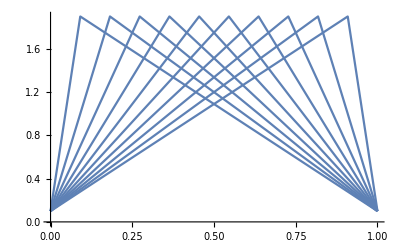

```mathematica
Plot[Table[PDF[fs[[i]],x],{i,1,10}],{x,0,1}]
```

The following function takes in the multipliers and the index of an agent. It then computes the probability that the largest scaled utility drawn comes from the first agent’s distribution.

```mathematica
probmax[mults_,i_]:=Integrate[PDF[fs[[i]],x]/CDF[fs[[i]],x]*Product[CDF[fs[[j]],mults[[i]]/mults[[j]]*x],{j,1,10}],{x,0,1}]
```

The next function takes in input as above, but computes the expected utility conditional on the agent having the largest scaled utility.

```mathematica
condexputil[mults_,i_]:=Integrate[x*PDF[fs[[i]],x]/CDF[fs[[i]],x]*Product[CDF[fs[[j]],mults[[i]]/mults[[j]]*x],{j,1,10}],{x,0,1}]/probmax[mults,i]
```

Multipliers generated in Python to equalize the probabilities:

```mathematica
multipliers=Map[Rationalize[#,0]&,{1.2726175697325768,1.2509468869501263,1.2280259678835055,1.2035666405375438,1.1771171046501063,1.1480599113933088,1.1157162129209264,1.0797915094362665,1.0408065736421024,1.0}]
```

{68598405/53903393,95502438/76344119,156153509/127158149,51296476/42620387,75773015/64371688,78196411/68111786,84795761/76001191,69406857/64278017,280983549/269967116,1}

Using these multipliers, measure how far the resulting probabilities deviate from the optimal point of 1/10, which is always at most 7.2*10^-6, and therefore less than the requested accuracy.

```mathematica
N[Max[Table[Abs[probmax[multipliers,i]-1/10],{i,1,10}]]]
```

7.2237×10^-6

Finally, we check the difference between the expected utility of agent i for an item conditioned on i receiving the item and i’s expected utility for an item without conditioning.

```mathematica
Table[N[condexputil[multipliers,i]-Expectation[x,x\[Distributed]fs[[i]]]],{i,1,10}]
```

{0.429462,0.406612,0.383949,0.361474,0.339192,0.31719,0.296051,0.27759,0.26497,0.261396}